#### Define Functions

```mathematica
Clear["Global`*"]
(*Gamma function and its values at zero*)
γ[η_,m_,n_]:=Abs[1-(1-((η+1)/2)^2)^m]^n
γ01[m_,n_]:=γ[0,m,n]
γ02[m_,n_]:=γ[0,m,n]
NAG3one[η_,m_,n_]:=(-γ01[m,n]+(γ01[m,n]-1) η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3two[η_,m_,n_]:=(1+η-2 γ[η,m,n])/(1-2 γ01[m,n])
NAG3three[η_,m_,n_]:=(-γ01[m,n]-γ01[m,n] η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3t2one[η_,m_,n_]:=NAG3three[-η,m,n]
NAG3t2two[η_,m_,n_]:=NAG3two[-η,m,n]
NAG3t2three[η_,m_,n_]:=NAG3one[-η,m,n]
(*Shape function for AG type 1*)
NShape[η_,m_,n_]:={NAG3one[η,m,n],NAG3two[η,m,n],NAG3three[η,m,n]};
dNShape[η_,m_,n_]:=D[NShape[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(*Shape function for AG type 2*)
NShape2[η_,m_,n_]:={NAG3t2one[η,m,n],NAG3t2two[η,m,n],NAG3t2three[η,m,n]};
dNShape2[η_,m_,n_]:=D[NShape2[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(***************************************************************)
(*Function to get the M matrices: relate Nodal force and Nodal traction*)
elementMmatrix[xpos_,AGtype_]:= Module[{},
{m,n,type}={AGtype[[1]],AGtype[[2]],AGtype[[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
(*Print[AGshape[η,m,n]];*)
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
M=Table[NIntegrate[AGshape[η,m,n][[j]]*AGshape[η,m,n][[i]]*jac,{η,-1,1}],{i,1,3},{j,1,3}]
];
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
GlobalMmat[xcoord_,conns_,AGtype_]:=Module[{n=Max@Flatten@conns,GlobalMat,Me,conn},
GlobalMat=ConstantArray[0.,{n,n}];
Do[
Me=elementMmatrix[xcoord[[e]],AGtype[[e]]];
(*Print[Me//MatrixForm];*)
conn=conns[[e]];
Do[
GlobalMat[[conn[[i]],conn[[j]]]]+=Me[[i,j]],{i,3},{j,3}],
{e,Length@conns}];
GlobalMat  (* <--return M assembled*)
]
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
PxinterpolatedData[Pvec_,AGtype_,xcoord_]:=Module[{},
Pxdata={};
(*total=0;*)
Pelem=Partition[Pvec,3,2];
nelem= Length[conns];
Do[
elem=e;
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};
If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
Clear[x,η];
xη=AGshape[η,1,1].xcoord[[elem]];
ηmap=η/.NSolve[xη==x,η]//First;
ηbranches=η/. Solve[xη==x,η];
x0=xcoord[[elem]][[1]]+0.01;
vals0=N[ηbranches/. x->x0];
(* ->something like {-1.4...,-0.6...}*)
(*pick the correct branch by "in parent domain" criterion*)
ηmap=First@Pick[ηbranches,(-1<=#<=1)&/@vals0];

PinterpolatePhysical=Sum[AGshape[η,m,n][[i]]*Pelem[[elem]][[i]],{i,1,3}]/.{η->ηmap};(*geometric mapping*)
(*resultant=NIntegrate[PinterpolatePhysical,{x,xmin,xmax}];
PxResultant=total+resultant;*)

{xmin,xmax}={Min[xcoord[[elem]]],Max[xcoord[[elem]]]};
n=30;
dx=(xmax-xmin)/n;
xdata=Table[xmin+i dx,{i,0,n}];
pdata=PinterpolatePhysical/.x->xdata;
plotdata=Transpose[{xdata, pdata}];
Pxdata=AppendTo[Pxdata, plotdata];
,{e,1,nelem}];
(*Print[PxResultant];*)
Flatten[Pxdata,1]
]


ComputeResultant[Pelem_,xcoord_,AGtype_]:=Module[{},
totalResutant=0;
Do[
elem=e;
xpos=xcoord[[elem]];
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];

resultant=Pelem[[elem]].NIntegrate[AGshape[η,m,n]*jac,{η,-1,1}];
(*Print[resultant];*)
totalResutant=totalResutant+resultant;
,{e,1,Length[conns]}];
totalResutant
]
```

#### p(x) y=10

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";

filename="nodal_displacement_disp_control_(1,10).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
topedge=raw[[6481;;6561]];

xcoordglobal=topedge[[All,2]];
Fy=topedge[[All,7]]
```

{1.39698×10^-9,5.82077×10^-9,-2.79397×10^-9,-4.65661×10^-9,-8.84756×10^-9,2.21189×10^-8,-9.31323×10^-9,-4.65661×10^-9,4.65661×10^-9,-1.86265×10^-9,1.07102×10^-8,-1.25729×10^-8,-9.77889×10^-9,-2.70084×10^-8,2.93367×10^-8,-2.09548×10^-8,1.21072×10^-8,-3.21306×10^-8,2.37487×10^-8,-9.77889×10^-9,2.42144×10^-8,-2.23517×10^-8,-2.04891×10^-8,-4.09782×10^-8,8.3819×10^-9,6.51926×10^-9,1.76951×10^-8,2.04891×10^-8,-6.0536×10^-8,-5.21541×10^-8,-1.37836×10^-7,2.08616×10^-7,-3.34069×10^6,-1.37205×10^7,1.16778×10^6,-4.18072×10^6,-1.87877×10^6,-3.57105×10^6,-1.70147×10^6,-3.34889×10^6,-1.65342×10^6,-3.34889×10^6,-1.70147×10^6,-3.57105×10^6,-1.87877×10^6,-4.18072×10^6,1.16778×10^6,-1.37205×10^7,-3.34069×10^6,3.57628×10^-7,8.56817×10^-8,-7.35745×10^-8,9.31323×10^-10,-1.21072×10^-8,-1.02445×10^-8,2.468×10^-8,-2.42144×10^-8,-4.65661×10^-10,1.21072×10^-8,0.,-2.32831×10^-9,1.90921×10^-8,1.81608×10^-8,-1.25729×10^-8,-5.12227×10^-9,-2.18861×10^-8,0.,-3.72529×10^-9,1.16415×10^-8,-3.0268×10^-8,-1.95578×10^-8,1.11759×10^-8,4.19095×10^-9,8.3819×10^-9,-4.65661×10^-9,-1.28057×10^-8,-6.0536×10^-9,-1.86265×10^-9,6.0536×10^-9,-1.14087×10^-8,0.}

Nodal traction vectors P(1,1) = {-0.000,0.000,-0.000,0.000,-0.001,0.001,-0.005,0.004,-0.030,0.025,-0.173,0.148,-1.009,0.861,-5.881,5.020,-34.278,29.258,-199.787,170.529,-1164.445,993.916,-6786.881,5792.965,-39556.843,33763.877,-230554.174,196790.297,-1.344×10^6,1.147×10^6,-7.832×10^6,8.490×10^6,-2.531×10^8,-4.540×10^7,-2.071×10^7,-2.609×10^7,-2.138×10^7,-2.158×10^7,-2.025×10^7,-2.011×10^7,-1.981×10^7,-2.011×10^7,-2.025×10^7,-2.158×10^7,-2.138×10^7,-2.609×10^7,-2.071×10^7,-4.540×10^7,-2.531×10^8,8.490×10^6,-7.832×10^6,1.147×10^6,-1.344×10^6,196790.297,-230554.174,33763.877,-39556.843,5792.965,-6786.881,993.916,-1164.445,170.529,-199.787,29.258,-34.278,5.020,-5.881,0.861,-1.009,0.148,-0.173,0.025,-0.030,0.004,-0.005,0.001,-0.001,0.000,-0.000,0.000,-0.000}

p(x) resultant force P(1,1) = -6.28021×10^7

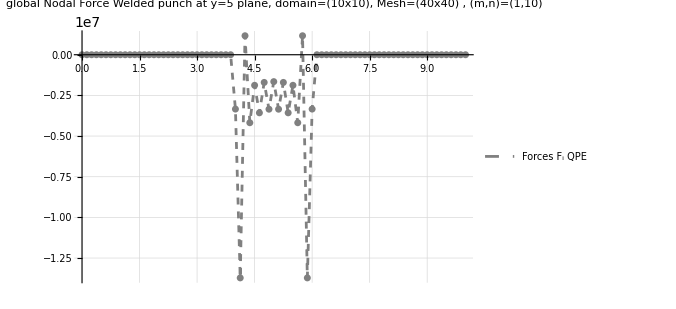

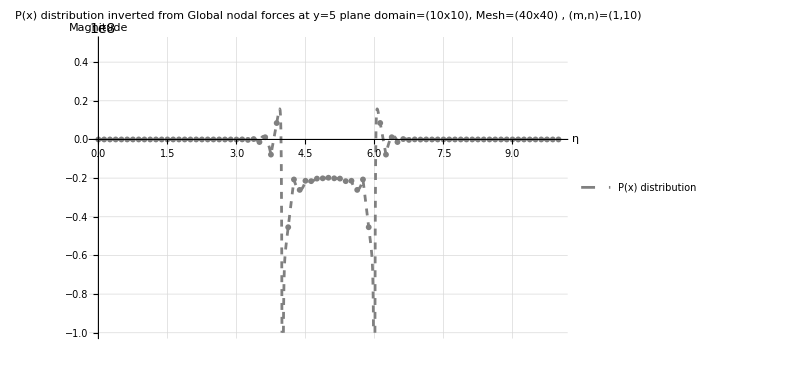

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[16]]={m1,n1,m2,n2, 1};
AGtype[[17]]={m1,n1,m2,n2, 2};

AGtype[[24]]={m1,n1,m2,n2, 1};
AGtype[[25]]={m1,n1,m2,n2, 2};

(*AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};*)

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];   (*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)

Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
(*Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]*)

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,{-1*10^8,5*10^7}},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```